```mathematica
(* load donut.nb first *)
```

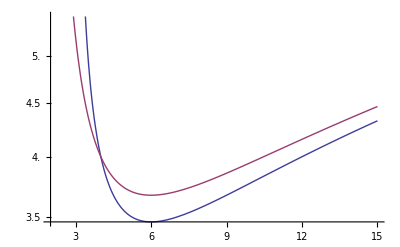

```mathematica
(* Keplerian profiles *)
utK[r_,a_]:=(r^2-2 r+a √r)/(r √(r^2-3r+2a √r))
uphiK[r_,a_]:=(r^2-2 a √r+a^2)/(√r √(r^2-3r+2a √r))
ellK[r_,a_]:=uphiK[r,a]/utK[r,a]
LogPlot[{uphiK[r,0],ellK[r,0]},{r,2,15}]
rmax[ellin_,a_]:=Quiet[NSolve[ellK[r,a]==ellin,r,Reals]][[2,1,2]]
```

```mathematica
α=0.1;
mdot=1;
myH=.3myR;
myΣ=1 10^4;

α=0.1;
mdot=10;
myH=.5myR;
myΣ=6 10^3;

α=0.1;
mdot=100;
myH=.65myR;
myΣ=12 10^3;

MBH=10;
a=0;
myell=7.3657;
Rg=MBH 147700;
MdEdd=MBH 2.23 10^18;
Mdot=mdot MdEdd;
myR=rmax[myell,0]
myvr=Mdot/(-2 π myR Rg myΣ)
myUTPOT=Abs[UTPOTatRH[myell,4/3,10^3,a,myR,myH]][[1]]
myKKK=KKKfromsigma[MBH,myell,myUTPOT,4/3,a,myR,myΣ][[1,1,2]]
```

50.0001

-4.00491×10^8

0.997962

4676.51

```mathematica
donutrhd[MBH,myell,myUTPOT,4/3,myKKK,a,myR,π/2]
```

{6.53086×10^-17,4.14466×10^-22,3.82142×10^-22,0.92201}